```mathematica
map1=Rasterize[Graphics[{Antialiasing->False,Black,Thickness[0.05],Line[{{1,1},{20,1},{20,20},{1,20},{1,1}}],
Line[{{1,5},{20,10}}],
Line[{{1,6},{20,11}}]
}],RasterSize->{20,20}]
```

-Graphics-

```mathematica
map1=(map1/.Graphics->List)[[1,1]]/.{{0,0,0}->1,{255,255,255}->0};
```

```mathematica
map1[[5,5]]=2;
map1[[15,15]]=3;
```

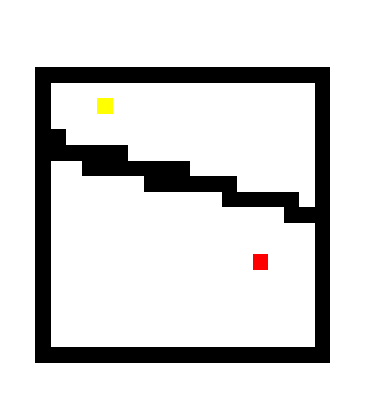

```mathematica
ArrayPlot[map1,ColorRules->{0->White,1->Black,2->Yellow,3->Red}]
```